# Titanic data classifier evaluation

## Introduction

In this notebook we show how to evaluate a classifier using ROC functions.

Load the paclet

```mathematica
Needs["AntonAntonov`ROCFunctions`"]
```

## Data ingestion

```mathematica
ExampleData[{"MachineLearning","Titanic"}]
```

Titanic Survival

```mathematica
dsTitanic=ResourceFunction["ExampleDataset"][{"MachineLearning","Titanic"}];
dsTitanic[1;;-1;;300]
```

## Classifier

Make classification data:

```mathematica
data=Map[Most[#]->Last[#]&,List@@@Normal[dsTitanic[Values]]];
```

Split data into training and testing parts:

```mathematica
SeedRandom[111];
{dataTraining,dataTesting}=TakeDrop[data,Floor[Length[data]*0.7]];
```

Make a classifier:

```mathematica
cf=Classify[dataTraining,Method->"NearestNeighbors"]
```

ClassifierFunction[…]

## Classification results

Get classification results over test data:

```mathematica
dsRes=
Dataset@Map[
Join[
<|"died"->0,"survived"->0|>,
cf[#[[1]],"Probabilities"],
<|"Predicted"->cf[#[[1]]],"Actual"->#[[2]]|>
]&,dataTesting];
dsRes[1;;4]
```

## ROC functions application

Convert the classification results into ROC associations:

```mathematica
thRange=Range[0,1,0.025];lsROCs=Table[ToROCAssociation[{"died","survived"},Normal@dsRes[All,"Actual"],Map[If[#>=th,"survived","died"]&,Normal[dsRes[All,"survived"]]]],{th,thRange}];
```

Make ROC plot:

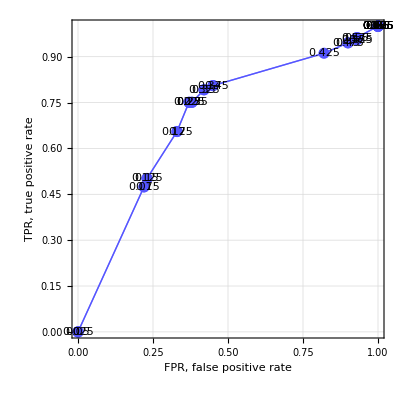

```mathematica
ROCPlot[thRange,lsROCs,"PlotJoined"->Automatic,"ROCPointCallouts"->True,"ROCPointTooltips"->True,PlotRange->All,GridLines->Automatic]
```

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

AntonAntonov/ROCFunctions

AntonAntonov`ROCFunctions`

AntonAntonov/ROCFunctions/tutorial/Titanicdataclassifierevaluation

### Keywords